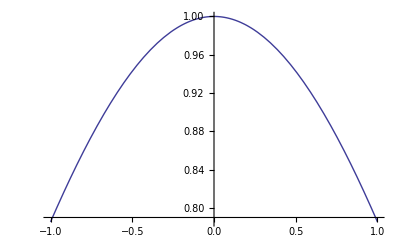

```mathematica
Needs["FunctionApproximations`"]
Plot[Cos[x*Pi/2]/(1-x^2),{x,-1,1}]
```

```mathematica
(MiniMaxApproximation[Cos[Pi*x/2]/(1-x^2),{x,{-0.999,0.999},3,0},PlotFlag->True&&PrintFlag->true&&MaxIterations->50])
```

{{-0.999,-0.723467,-4.36515×10^-15,0.723467,0.999},{0.997383+1.65984×10^-16 x-0.214077 x^2-1.48849×10^-16 x^3,0.00261658}}

```mathematica
MiniMaxApproximation[1/2 Erfc[-x/(√2)],{x,{0,5},4,5},Brake->{10,10}&&MaxIterations->500][[2,1]]
```

MiniMaxApproximation::conv: Warning: convergence was not complete.

(0.500006+0.258306 x+0.0131948 x^2+0.0067541 x^3+0.013347 x^4)/(1-0.28077 x+0.247371 x^2-0.0444257 x^3+0.0189689 x^4-0.00024807 x^5)

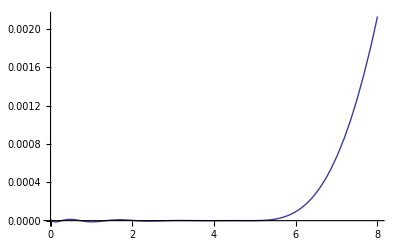

```mathematica
Plot[Log[%23/(1/2 Erfc[-x/(√2)])],{x,0,8} ,PlotRange->Full]
```

```mathematica
floom[y]
```

```mathematica
psi=HornerForm[MiniMaxApproximation[(1/2 Erfc[-x/(√2)]-1/2)/x,{x,{0.1,5},3,5},Bias->-0][[2,1]]*x]
```

(x (-664.282+x (211.052+(-54.6369-3.13535 x) x)))/(-1665.13+x (529.232+x (-414.991+x (80.874+x (-28.0145+1. x)))))

```mathematica
HornerForm[MiniMaxApproximation[(1/2 Erfc[-x/(√2)]-1/2)/x,{x,{0.05,5},4,5}][[2,1]]*x]
```

(x (-6738.03+x (2057.05+x (-551.013+(-30.5159-4.29621 x) x))))/(-16889.6+x (5153.98+x (-4185.16+x (762.029+x (-271.851+1. x)))))

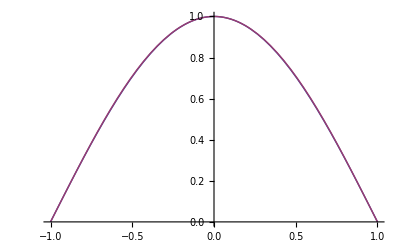

```mathematica
Plot[{Cos[x*Pi/2],1+(Pi/4-2)*x^2+(1-Pi/4)*x^4},{x,-1,1}]
```

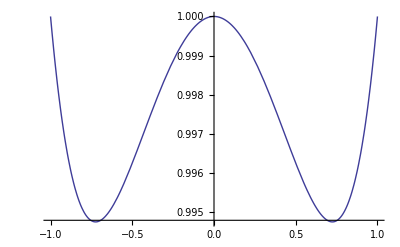

```mathematica
Plot[Cos[x*Pi/2]/(1+(Pi/4-2)*x^2+(1-Pi/4)*x^4),{x,-1,1}]
```

```mathematica
N[HornerForm[(1+(Pi/4-2)*x^2+(1-Pi/4)*x^4),x]]
```

1.+x^2 (-1.2146+0.214602 x^2)

1.+x^2 (-1.2146+0.214602 x^2)

1.+x^2 (-1.2146+0.214602 x^2)

```mathematica
Log10[0.994^2]*10
```

-0.0522723

```mathematica
-0.0261361560268669
```

-0.0261362

```mathematica
g[x_]:=Cos[Pi*x/2]
g[1]
```

```mathematica
0
gd[x_]=D[g[x],x]
```

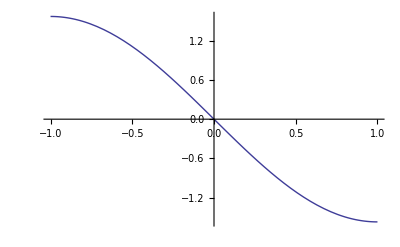

```mathematica
Plot[gd[x],{x,-1,1}]
```

```mathematica
N[HornerForm[Simplify[InterpolatingPolynomial[{{-1,g[-1],gd[-1]},{-2/3,g[-2/3],gd[-2/3]},{0,g[0],gd[0]},{2/3,g[2/3],gd[2/3]},{1,g[1],gd[1]}},x]]] ]
```

1.+x^2 (-1.2337+x^2 (0.253639+x^2 (-0.0207919+0.000848933 x^2)))

```mathematica
N[HornerForm[Simplify[InterpolatingPolynomial[{{-1,g[-1],gd[-1]},{0,g[0],gd[0]},{1,g[1],gd[1]}},x]]],18]
```

1.+x^2 (-1.21460183660255169+0.21460183660255169 x^2)

```mathematica
h[x_]:=Sqrt[Cos[Pi*x/2]]
```

```mathematica
hd[x_]=D[h[x],x]
```

```mathematica
-(π Sin[(π x)/2])/(4 √Cos[(π x)/2])
```

-(π Sin[(π x)/2])/(4 √Cos[(π x)/2])

```mathematica
happrox[x_]:=HornerForm[Simplify[
InterpolatingPolynomial[{{-1,h[-1],Automatic},{-2/3,h[-2/3],hd[-2/3]},{0,h[0],hd[0]},{2/3,h[2/3],hd[2/3]},{1,h[1],Automatic}},x]
]]
```

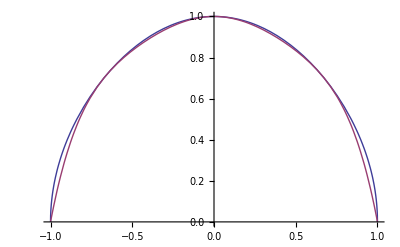

```mathematica
Plot[{h[x],happrox[x]},{x,-1,1}]
```

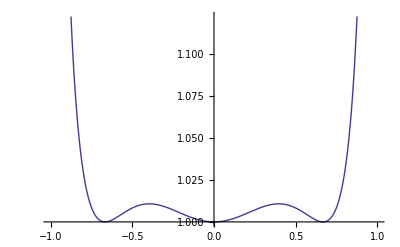

```mathematica
Plot[{h[x]/happrox[x]},{x,-1,1}]
```

```mathematica
N[happrox[x],18]
```

1.+x^2 (-0.764879340394491635+x^2 (0.616868399844512129-0.851989059450020494 x^2))

```mathematica
Log10[1.02^2]*10
```

0.172003

```mathematica
HornerForm[Simplify[
MiniMaxApproximation[h[x],{x,-1,1}]
]]
```

```mathematica
MiniMaxApproximation[h[x],{x,{-1,1}, 6,2},PlotFlag->True]
```

MiniMaxApproximation::extalt: The extrema of the error do not alternate in sign.  It may be that MiniMaxApproximation has lost track of the extrema by going too fast. If so try increasing the values in the option Brake. It may be that the WorkingPrecision is insufficient. Otherwise there is an extra extreme value of the error, and MiniMaxApproximation cannot deal with this problem.

{{-1.,-0.97023,-0.812856,-0.549108,-0.233785,0.233785,0.549108,0.812856,0.97023,1.},(1.+3.72906×10^-17 x-1.46392 x^2+6.20547×10^-16 x^3+0.451413 x^4-6.37467×10^-16 x^5+0.0248248 x^6)/(1.+2.55857×10^-16 x-0.847755 x^2),{-1.03375×10^7,0.0230222,-0.000849665,0.000100343,-0.0000177858,-0.0000177858,0.000100343,-0.000849665,0.0230222,-1.03375×10^7}}

```mathematica
Plot[{h[x]/happrox2[x]},{x,-1,1}]
```

General::ivar: -0.999959 is not a valid variable.

General::stop: Further output of General :: ivar will be suppressed during this calculation.

Part::partd: Part specification NRoots[False, -0.999959] ⟦ 1, 2 ⟧ is longer than depth of object.

Part::partd: Part specification NRoots[False, -0.999959] ⟦ 2, 2 ⟧ is longer than depth of object.

MiniMaxApproximation::dervnotnum: {0.00801113, ∂_-0.999959 0.00801113, ∂_-0.999959 ∂_-0.999959 0.00801113} is not numerical at -0.999959 = {-0.900969, -0.62349, -0.222521, 0.222521, 0.62349, 0.900969} : {{0.00801113, 0.00801113, 0.00801113, 0.00801113, 0.00801113, 0.00801113}, {« 1 »}, {∂_-0.900969 ∂_-0.900969 0.00801113, « 4 », ∂_0.9009688679024191` ∂_« 19 » 0.00801113}}.

ReplaceAll::reps: {-0.999959} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partd: Part specification NRoots[False, -0.959143] ⟦ 1, 2 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

MiniMaxApproximation::dervnotnum: {0.253247, ∂_-0.959143 0.253247, ∂_-0.959143 ∂_-0.959143 0.253247} is not numerical at -0.959143 = {-0.900969, -0.62349, -0.222521, 0.222521, 0.62349, 0.900969} : {{0.253247, 0.253247, 0.253247, 0.253247, 0.253247, 0.253247}, {« 1 »}, {∂_-0.900969 ∂_-0.900969 0.253247, « 4 », ∂_0.9009688679024191` ∂_« 19 » 0.253247}}.

ReplaceAll::reps: {-0.959143} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

MiniMaxApproximation::dervnotnum: {0.357688, ∂_-0.918326 0.357688, ∂_-0.918326 ∂_-0.918326 0.357688} is not numerical at -0.918326 = {-0.900969, -0.62349, -0.222521, 0.222521, 0.62349, 0.900969} : {{0.357688, 0.357688, 0.357688, 0.357688, 0.357688, 0.357688}, {« 1 »}, {∂_-0.900969 ∂_-0.900969 0.357688, « 4 », ∂_0.9009688679024191` ∂_0.9009688679024191` 0.357688}}.

General::stop: Further output of MiniMaxApproximation :: dervnotnum will be suppressed during this calculation.

ReplaceAll::reps: {-0.918326} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

-Graphics-

```mathematica
j[x_]:=Sin[Pi*x/2];
jd[x_]=D[j[x],x];
japprox[x_]:=HornerForm[Simplify[InterpolatingPolynomial[{{-1,j[-1],Automatic},{0,j[0],jd[0]},{1,j[1],Automatic}},x]]]
japprox[x]
```

x (π/2+(1-π/2) x^2)

```mathematica
N[japprox[x],18]
```

x (1.57079632679489662-0.570796326794896619 x^2)